```mathematica
Clear[a,b];
a=1;b=2;
```

```mathematica
a
```

1

```mathematica
b
```

2

```mathematica
swap[a_,b_]:=(a=2;3);
(*Module[
{},
Head[a]
]*)
```

```mathematica
1=2;
```

```mathematica
swap[1,b]
```

3

```mathematica
swap[a,b]
```

3

```mathematica
SetAttributes[swap]={HoldAll};
```

```mathematica
swap[a,b]
```

3

### Mathematica implementation of swap via symbols

```mathematica
Remove[a,b,swap1,swap2];
```

```mathematica
a=1;b=2;
```

```mathematica
swap1[a_,b_]:=Module[
{temp},
temp=a;
b=a;
a=temp;
]
```

```mathematica
swap1[a,b]
```

```mathematica
SetAttributes[swap2,HoldAll];
swap2[a_,b_]:=f@Module[
{temp},
temp=a;
a=b;
b=temp;
]
```

```mathematica
swap2[a,b]
```

```mathematica
a
b
```

2

1

```mathematica
tr=swap2[a,b]//Trace(*//TableForm[#]&*)
```

{swap2[a,b],f[Module[{temp$},temp$=a;a=b;b=temp$;]],{Module[{temp$},temp$=a;a=b;b=temp$;],{temp$30209=a;a=b;b=temp$30209;,{{a,1},temp$30209=1,1},{{b,2},a=2,2},{{temp$30209,1},b=1,1},Null},Null},f[Null]}

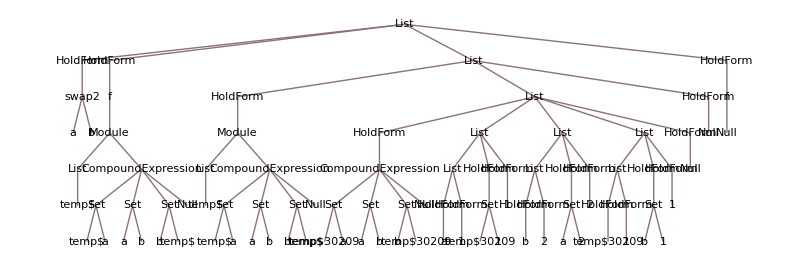

```mathematica
tr//TreeForm[#,ImageSize-> 800]&
```